-Graphics-

-Graphics-

-Graphics-

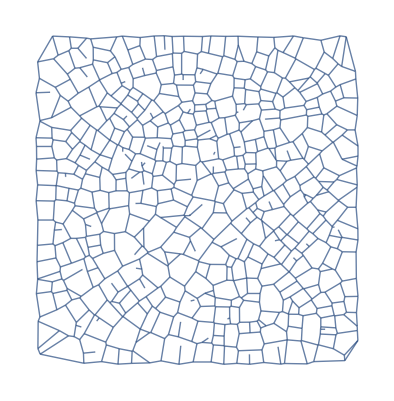

-Graphics-

```mathematica
Clear[g1,g2]
g1=ColorNegate[DeleteSmallComponents[-Graphics-,300]]
DeleteSmallComponents[%,300]
 
  Thinning[%,6]
(* g2=MorphologicalGraph[%, EdgeStyle->{Red,Thick},VertexStyle->Red] *)   
g2=MorphologicalGraph[%, VertexStyle->Red]    
Show[g1,g2]
```